## Cholesky

```mathematica
Cholesky[A_]:=(
n=Length[A];
L=Table[0,{i,n},{j,n}];
For[k=1, k≤n, k++, (*Iterate over the columns*) 
(*Find the diagonal element*)
L[[k,k]]=√(A[[k,k]]-Sum[L[[k,p]]^2,{p,1,k-1}]);
For[j=k+1,j≤n,j++, (*Find all the elements below the main diagonal*)
L[[j,k]]=1/L[[k,k]](A[[k,j]]-Sum[L[[k,i]]L[[j,i]],{i,1,k-1}])
]
];
L
)
```

```mathematica
L=Cholesky[{{10,45,285},{45,285,2025},{285,2025,15333}}]
```

{{√10,0,0},{9 √(5/2),√(165/2),0},{57 √(5/2),9 √(165/2),4 √33}}

```mathematica
L.Transpose[L]
```

{{10,45,285},{45,285,2025},{285,2025,15333}}

## Least-squares method

### LUSolve

```mathematica
LUSolve[L_,U_,b_]:=(
Module[{x,y}, (*Define x and y to be local variables*)
n=Length[b];
y=Table[0,{i,n}] ;
For[i=1,i≤n, i++,
y[[i]]=1/L[[i,i]](b[[i]]-Sum[L[[i,j]]y[[j]],{j,1,i-1}])

];
x=Table[0,{i,n}] ;
For[i=n,i≥1, i--,
x[[i]]=1/U[[i,i]](y[[i]]-Sum[U[[i,j]]x[[j]],{j,i+1,n}])

];
x
])
```

### Least-squares fit for the falling body problem

```mathematica
t=Range[0,9];
X=Table[{1,t[[i]],t[[i]]^2},{i,1,10}];
y={{450,445,431,408,375,332,279,216,143,61}}//Transpose;
A=Transpose[X].X//N;
b=Transpose[X].y//N;
L=Cholesky[A];
coefs=LUSolve[L,Transpose[L],b]
```

{{449.364},{0.962121},{-4.90152}}

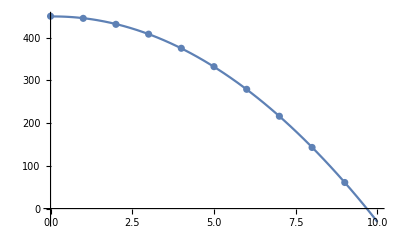

```mathematica
p[x_]={{1,x,x^2}}.coefs;
plot1=Plot[p[x],{x,0,10}];
plot2=ListPlot[Table[{t[[i]],y[[i,1]]},{i,10}]];
Show[plot1,plot2]
```